# Full model simple

### The system is described by the following equations:

```mathematica
Clear[s,hmax,rmax,shh,ma,mh,k]
ds = rmax*s*(1-s/k)-s*(ma+mh*hmax*shh/(shh+s));
dca = alpha*hca/(hca+(hmax*shh/(shh+s)))-ca*(pda+pea+pba);
dcs =beta*s-cs*(pds+pes+pbs);
dcb = pba*ca+pbs*cs-pdb*cb;
```

```mathematica
sol = Simplify[Solve[{ds==0},{s}]]
```

{{s→0},{s→(-k ma+k rmax-rmax shh+√(-4 k (ma+hmax mh-rmax) rmax shh+(k (ma-rmax)+rmax shh)^2))/(2 rmax)},{s→-(k ma-k rmax+rmax shh+√(-4 k (ma+hmax mh-rmax) rmax shh+(k (ma-rmax)+rmax shh)^2))/(2 rmax)}}

```mathematica
paramvalues={rmax->1.2,shh->1,ma->0.25,mh->0.05,k->6};
solution=sol[[2,1,2]]/.paramvalues;
hmaxValue=hmax/. FindRoot[solution==0,{hmax,0,50}]
```

33.6424+0.0640634 ⅈ

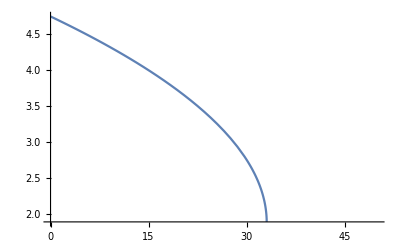

```mathematica
Plot[solution,{hmax,0,50}]
```

```mathematica
paramvalues={rmax->1.2,shh->1,ma->0.25,mh->0.05,k->6, hmax->33.063};
solution=sol[[2,1,2]]/.paramvalues
```

1.875+0.0111803 ⅈ

```mathematica
paramvalues={rmax->1.2,shh->1,ma->0.25,mh->0.05,k->6};
solution=sol[[3,1,2]]/.paramvalues;
hmaxValue=hmax/. FindRoot[solution==0,{hmax,0,50}]
```

19.-3.89175×10^-13 ⅈ

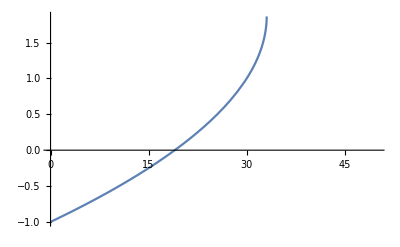

```mathematica
Plot[solution,{hmax,0,50}]
```

```mathematica
paramvalues={rmax->1.2,shh->1,ma->0.25,mh->0.05,k->6, hmax->18.9};
solution=sol[[3,1,2]]/.paramvalues
```

-0.00665486

```mathematica
assumptions=And[rmax>0,k>0,shh>0,ma>0,ma<=1,mh>0,mh<=1];
Assuming[assumptions, FullSimplify[sol[[1]][[1]][[2]]>=0]]
```

True

```mathematica
Assuming[assumptions, FullSimplify[sol[[2]][[1]][[2]]>=0]]
```

k rmax+√(-4 k (ma+hmax mh-rmax) rmax shh+(k (ma-rmax)+rmax shh)^2)≥k ma+rmax shh

```mathematica
Assuming[assumptions, FullSimplify[sol[[3]][[1]][[2]]>=0 && sol[[2]][[1]][[2]]>=0]]
```

k ma+rmax shh+√(-4 k (ma+hmax mh-rmax) rmax shh+(k (ma-rmax)+rmax shh)^2)≤k rmax&&k rmax+√(-4 k (ma+hmax mh-rmax) rmax shh+(k (ma-rmax)+rmax shh)^2)≥k ma+rmax shh

```mathematica
reducedResult=TimeConstrained[Reduce[sol[[3]][[1]][[2]]>0&&sol[[2]][[1]][[2]]>0&&assumptions],600];
simplifiedResult=Simplify[LogicalExpand[reducedResult&&assumptions],assumptions]
```

(ma<rmax||rmax>1)&&rmax<ma+hmax mh&&k>(rmax shh)/(-ma+rmax)&&2 k (ma+2 hmax mh-rmax) rmax shh≤k^2 (ma-rmax)^2+rmax^2 shh^2

```mathematica
reducedResult=TimeConstrained[Reduce[sol[[3]][[1]][[2]]>0&&assumptions],600];
simplifiedResult=Simplify[LogicalExpand[reducedResult&&assumptions],assumptions]
```

(ma<rmax||rmax>1)&&rmax<ma+hmax mh&&k>(rmax shh)/(-ma+rmax)&&2 k (ma+2 hmax mh-rmax) rmax shh≤k^2 (ma-rmax)^2+rmax^2 shh^2

### Parameter value test

```mathematica
Manipulate[Module[{sol1,sol2, sol3},

sol1 = 0;

sol2=(-k ma+k rmax-rmax shh+√(-4 k (ma+hmax mh-rmax) rmax shh+(k (ma-rmax)+rmax shh)^2))/(2 rmax);

sol3=-(k ma-k rmax+rmax shh+√(-4 k (ma+hmax mh-rmax) rmax shh+(k (ma-rmax)+rmax shh)^2))/(2 rmax);

Plot[{sol1,sol2, sol3},{hmax,0,50},AxesLabel->{Style["Hmax", 14, Black],Style["S", 14, Black]},PlotLabel->Style["S equilibria", 16, Black],PlotLegends->{"equilibrium 1","equilibrium 2","equilibrium 3"},ImageSize->{800,400}]],{{rmax,1.2},0,50,0.1,Appearance->"Labeled",Assumptions->assumptions},{{shh,1},0,50,0.1,Appearance->"Labeled",Assumptions->assumptions},{{ma,0.25},0,1,0.1,Appearance->"Labeled",Assumptions->assumptions},{{mh,0.05},0,1,0.1,Appearance->"Labeled",Assumptions->assumptions},{{k,6},0,50,1,Appearance->"Labeled",Assumptions->assumptions},ControlPlacement->Left
]
```

### Bifurcation diagrams

```mathematica
seagrassColor=Darker[Green,0.5];
bistableColor=Directive[Dotted,Black,Dashing[{0.01}]];
bareColor=Darker[Yellow];

rmax=1.2;
k=6;
mh=0.05;
shh=1;
ma = 0.25;

seagrassLeft=(-k ma+k rmax-rmax shh+Sqrt[-4 k (ma+hmax mh-rmax) rmax shh+(k (ma-rmax)+rmax shh)^2])/(2 rmax);
seagrassRight=seagrassLeft;

bistable=If[(Im[-((k ma-k rmax+rmax shh+Sqrt[-4 k (ma+hmax mh-rmax) rmax shh+(k (ma-rmax)+rmax shh)^2])/(2 rmax))]==0)&&(-((k ma-k rmax+rmax shh+Sqrt[-4 k (ma+hmax mh-rmax) rmax shh+(k (ma-rmax)+rmax shh)^2])/(2 rmax))>0),-((k ma-k rmax+rmax shh+Sqrt[-4 k (ma+hmax mh-rmax) rmax shh+(k (ma-rmax)+rmax shh)^2])/(2 rmax)),None];
bare=If[-ma-hmax mh+rmax<=0,0,None];

plot=Show[Plot[seagrassLeft,{hmax,0,50},PlotStyle->seagrassColor],Plot[seagrassRight,{ma,0.5,1},PlotStyle->seagrassColor],Plot[bistable,{hmax,0,50},PlotStyle->bistableColor],Plot[bare,{hmax,0,50},PlotStyle->bareColor],Frame->True,FrameLabel->{Row[{Style["Maximum hydrodynamic (",16,Black],Style[Subscript[H,max],16,Black,Italic],Style[")",16,Black]}],Style["Seagrass (\!\(\*Italic\`S\))",16,Black]}
,FrameTicks->{{{0,1,2,3,4,5},None},{{0,10,20,30,40,50},None}},FrameTicksStyle->Directive[FontSize->14],Axes->False,PlotRange->{{0,50},{0,5}},AspectRatio->0.8,ImageSize->{1000,500}];

plot=Legended[plot,Placed[LineLegend[{seagrassColor,bistableColor,bareColor},{Style["Seagrass",16,Black],Style["Bistable",16,Black],Style["Bare",16,Black]},LegendLayout->{"Column",1},LegendFunction->None,LegendMargins->5, LabelStyle->{FontSize->16},LegendMarkerSize->20],{1.05,0.5}]]
```

-Graphics-

```mathematica
Export["",plot,ImageResolution->1000];
```

```mathematica
plot2=Module[{seagrassColor,bistableColor,bareColor,seagrassLeft,seagrassRight,bistable,bare,rmax,k,mh,shh,hmax,pda,pea,pba,alpha,hca,ma},seagrassColor=Darker[Orange];
bistableColor=Directive[Dotted,Darker[Orange],Dashing[{0.01}]];
bareColor=Darker[Orange];
rmax=1.2;
	k=6;
	mh=0.05;
	shh=1;
	ma = 0.25;
pda=0.05;
pea=0.2;
pba=0.01;
alpha=4;
hca=10;
seagrassLeft=1/(pda+pea+pba)*(alpha*hca/(hca+hmax*shh/(shh+(-k ma+k rmax-rmax shh+Sqrt[-4 k (ma+hmax mh-rmax) rmax shh+(k (ma-rmax)+rmax shh)^2])/(2 rmax))));
seagrassRight=seagrassLeft;
bistable=If[(Im[-((k ma-k rmax+rmax shh+Sqrt[-4 k (ma+hmax mh-rmax) rmax shh+(k (ma-rmax)+rmax shh)^2])/(2 rmax))]==0)&&(-((k ma-k rmax+rmax shh+Sqrt[-4 k (ma+hmax mh-rmax) rmax shh+(k (ma-rmax)+rmax shh)^2])/(2 rmax))>0),1/(pda+pea+pba)*(alpha*hca/(hca+hmax*shh/(shh+-((k ma-k rmax+rmax shh+Sqrt[-4 k (ma+hmax mh-rmax) rmax shh+(k (ma-rmax)+rmax shh)^2])/(2 rmax))))),None];
bare=If[-ma-hmax mh+rmax<=0,1/(pda+pea+pba)*(alpha*hca/(hca+hmax*shh/(shh))),None];
plot22=Show[Plot[seagrassLeft,{hmax,0,50},PlotStyle->seagrassColor],Plot[seagrassRight,{hmax,0,50},PlotStyle->seagrassColor],Plot[bistable,{hmax,0,50},PlotStyle->bistableColor],Plot[bare,{hmax,0,50},PlotStyle->bareColor],Frame->True,FrameLabel->{"",None},FrameTicks->{{{{0,"0"},{5,"5"},{10,"10"},{15,"15"},{20,"20"}},None},{{{0,"0"},{10,"10"},{20,"20"},{30,"30"},{40,"40"},{50,"50"}},None}},FrameTicksStyle->Directive[FontSize->14],Axes->False,PlotRange->{{0,50},{0,20}},ImageSize->{1000,500}]];

Legended[plot22,Placed[LineLegend[{Darker[Orange],bistableColor,bareColor},{"Allochtonous"},LegendLayout->{"Column",1},LegendFunction->None,LegendMargins->5],{1.05,0.5}]]
```

-Graphics-

```mathematica
plot3=Module[{seagrassColor,bistableColor,bareColor,seagrassLeft,seagrassRight,bistable,bare,rmax,k,mh,shh,hmax,pda,pea,pba,alpha,hca,ma},seagrassColor=Red;
bistableColor=Directive[Dotted,Red,Dashing[{0.01}]];
bareColor=Red;
rmax=1.2;
	k=6;
	mh=0.05;
	shh=1;
	ma = 0.25;
pda=0.05;
pea=0.2;
pba=0.01;
alpha=4;
hca=10;
beta=0.6;
pbs=0.01;
pes=0.2;
pds=0.05;
seagrassLeft=beta*(-k ma+k rmax-rmax shh+Sqrt[-4 k (ma+hmax mh-rmax) rmax shh+(k (ma-rmax)+rmax shh)^2])/(2 rmax)/(pds+pes+pbs);
seagrassRight=seagrassLeft;
bistable=If[(Im[-((k ma-k rmax+rmax shh+Sqrt[-4 k (ma+hmax mh-rmax) rmax shh+(k (ma-rmax)+rmax shh)^2])/(2 rmax))]==0)&&(-((k ma-k rmax+rmax shh+Sqrt[-4 k (ma+hmax mh-rmax) rmax shh+(k (ma-rmax)+rmax shh)^2])/(2 rmax))>0),beta*-((k ma-k rmax+rmax shh+Sqrt[-4 k (ma+hmax mh-rmax) rmax shh+(k (ma-rmax)+rmax shh)^2])/(2 rmax))/(pds+pes+pbs),None];
bare=If[-ma-hmax mh+rmax<=0,0,None];
plot33=Show[Plot[seagrassLeft,{hmax,0,50},PlotStyle->seagrassColor],Plot[seagrassRight,{hmax,0,50},PlotStyle->seagrassColor],Plot[bistable,{hmax,0,50},PlotStyle->bistableColor],Plot[bare,{hmax,0,50},PlotStyle->bareColor],Frame->True,FrameLabel->{"",None},FrameTicks->{{{{0,"0"},{5,"5"},{10,"10"},{15,"15"},{20,"20"}},None},{{{0,"0"},{10,"10"},{20,"20"},{30,"30"},{40,"40"},{50,"50"}},None}},FrameTicksStyle->Directive[FontSize->14],Axes->False,PlotRange->{{0,50},{0,20}},ImageSize->{1000,500}]];

Legended[plot33,Placed[LineLegend[{Red},{"Autochtonous"},LegendLayout->{"Column",1},LegendFunction->None,LegendMargins->5],{1.05,0.5}]]
```

-Graphics-

```mathematica
plot4=Module[{seagrassColor,bistableColor,bareColor,seagrassLeft,seagrassRight,bistable,bare,rmax,k,mh,shh,hmax,pda,pea,pba,alpha,hca,ma},seagrassColor=Purple;
bistableColor=Directive[Dotted,Purple,Dashing[{0.01}]];
bareColor=Purple;
rmax=1.2;
	k=6;
	mh=0.05;
	shh=1;
	ma = 0.25;
pda=0.05;
pea=0.2;
pba=0.01;
alpha=4;
hca=10;
beta=0.6;
pbs=0.01;
pes=0.2;
pds=0.05;
pdb=0.014;
seagrassLeft=(pba*1/(pda+pea+pba)*(alpha*hca/(hca+hmax*shh/(shh+(-k ma+k rmax-rmax shh+Sqrt[-4 k (ma+hmax mh-rmax) rmax shh+(k (ma-rmax)+rmax shh)^2])/(2 rmax))))+pbs*beta*(-k ma+k rmax-rmax shh+Sqrt[-4 k (ma+hmax mh-rmax) rmax shh+(k (ma-rmax)+rmax shh)^2])/(2 rmax)/(pds+pes+pbs))/pdb;
seagrassRight=seagrassLeft;
bistable=If[(Im[-((k ma-k rmax+rmax shh+Sqrt[-4 k (ma+hmax mh-rmax) rmax shh+(k (ma-rmax)+rmax shh)^2])/(2 rmax))]==0)&&(-((k ma-k rmax+rmax shh+Sqrt[-4 k (ma+hmax mh-rmax) rmax shh+(k (ma-rmax)+rmax shh)^2])/(2 rmax))>0),(pba*1/(pda+pea+pba)*(alpha*hca/(hca+hmax*shh/(shh+-((k ma-k rmax+rmax shh+Sqrt[-4 k (ma+hmax mh-rmax) rmax shh+(k (ma-rmax)+rmax shh)^2])/(2 rmax)))))+pbs*beta*-((k ma-k rmax+rmax shh+Sqrt[-4 k (ma+hmax mh-rmax) rmax shh+(k (ma-rmax)+rmax shh)^2])/(2 rmax))/(pds+pes+pbs))/pdb,None];
bare=If[-ma-hmax mh+rmax<=0,pba*1/(pda+pea+pba)*(alpha*hca/(hca+hmax*shh/(shh)))/pdb,None];
plot44=Show[Plot[seagrassLeft,{hmax,0,50},PlotStyle->seagrassColor],Plot[seagrassRight,{hmax,0,50},PlotStyle->seagrassColor],Plot[bistable,{hmax,0,50},PlotStyle->bistableColor],Plot[bare,{hmax,0,50},PlotStyle->bareColor],Frame->True,FrameLabel->{"",None},FrameTicks->{{{{0,"0"},{5,"5"},{10,"10"},{15,"15"},{20,"20"}},None},{{{0,"0"},{10,"10"},{20,"20"},{30,"30"},{40,"40"},{50,"50"}},None}},FrameTicksStyle->Directive[FontSize->14],Axes->False,PlotRange->{{0,50},{0,20}},ImageSize->{1000,500}]];

Legended[plot44,Placed[LineLegend[{Purple},{"Buried"},LegendLayout->{"Column",1},LegendFunction->None,LegendMargins->5],{1.05,0.5}]]
```

-Graphics-

```mathematica
mergedPlot=Show[Legended[plot22,Placed[LineLegend[{Darker[Orange],bistableColor,bareColor},{Style["Allochtonous (\!\(\*SubscriptBox[\(C\), \(A\)]\))",16,Black]},LegendLayout->{"Column",1},LegendFunction->None,LegendMargins->5],{1.05,0.5}]],Legended[plot33,Placed[LineLegend[{Red},{Style["Autochtonous (\!\(\*SubscriptBox[\(C\), \(S\)]\))",16,Black]},LegendLayout->{"Column",1},LegendFunction->None,LegendMargins->5],{1.05,0.5}]],Legended[plot44,Placed[LineLegend[{Purple},{Style["Buried (\!\(\*SubscriptBox[\(C\), \(B\)]\))",16,Black]},LegendLayout->{"Column",1},LegendFunction->None,LegendMargins->5],{1.05,0.5}]],PlotRange->{{0,50},{0,20}},AspectRatio->0.8,ImageSize->{1000,500},FrameLabel->{Row[{Style["Maximum hydrodynamic (",16,Black],Style[Subscript[H,max],16,Black,Italic],Style[")",16,Black]}],Style["Carbon (\!\(\*Italic\`C\))",16,Black]}]
```

-Graphics-

```mathematica
Export["",mergedPlot,ImageResolution->1000];
```

### Gradual hydrodynamic change

#### Seagrass

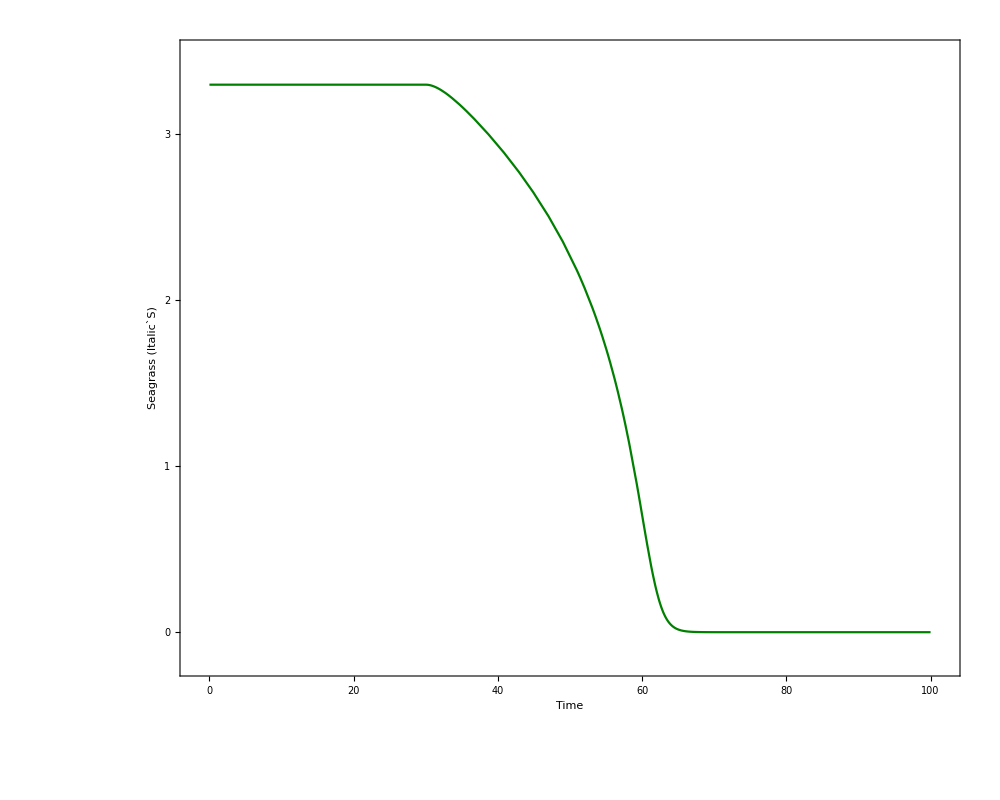
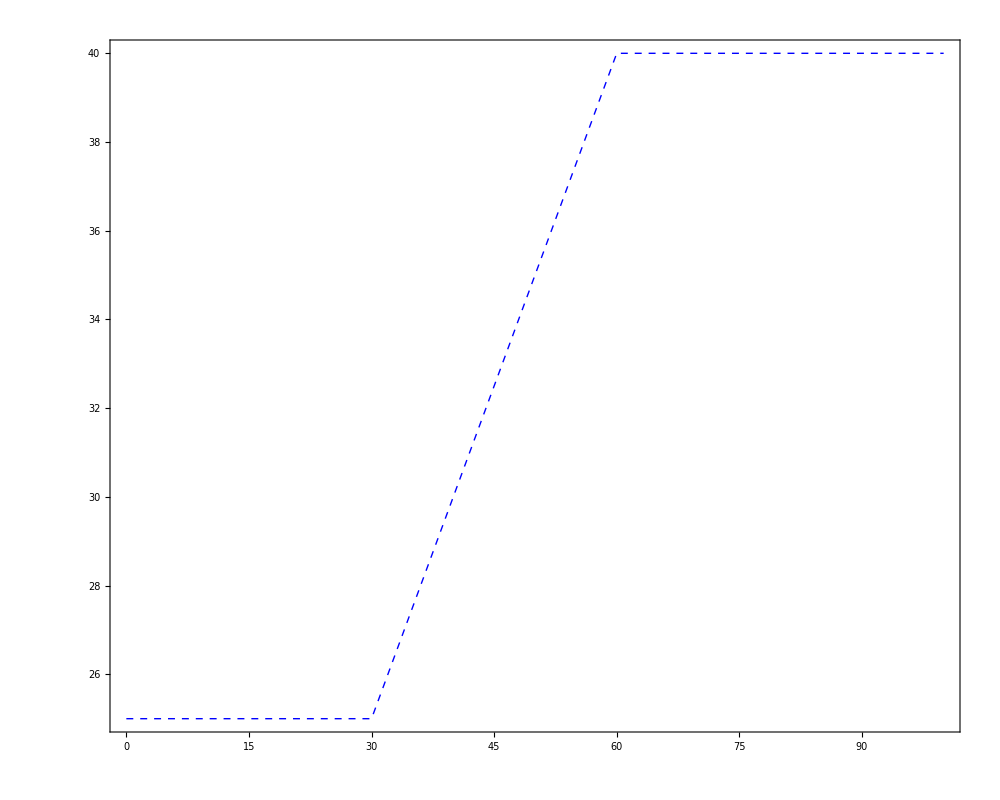

```mathematica
Clear[plt,sol,xrange,rmax,k,ma,mh,shh,hmax0,hmax1,t0,t1,s0,solexist,deriv,test,stableSolutions,greatestStableSolution,hmax]
Module[{plt,sol,xrange,rmax,k,ma,mh,shh,hmax0,hmax1,t0,t1,s0,solexist,deriv,test,stableSolutions,greatestStableSolution},

rmax=6/5;
k=6;
mh=1/20;
shh=1;
ma=1/4;

xrange=100;
t0=30;
t1=60;
hmax0=25;
hmax1=40;

ds=rmax*s*(1-s/k)-s*(ma+mh*hmax0*shh/(shh+s));
sol=Solve[{ds==0,Element[s,Reals]},{s}];
solexist=Select[sol,(#[[1,2]]>=0)&];
deriv=D[ds,s]/. solexist;
test=Map[#<=0&,deriv];
stableSolutions=Pick[solexist,test];
s0=MaximalBy[stableSolutions,#[[1,2]]&][[1,1,2]];

solint=NDSolve[{s'[t]==rmax*s[t]*(1-s[t]/k)-s[t]*(ma+mh*hmax[t]*shh/(shh+s[t])),hmax'[t]==Piecewise[{{0,0<=t<t0},{(hmax1-hmax0)/(t1-t0),t0<=t<t1},{0,t>=t1}}],s[0]==s0,hmax[0]==hmax0},{s,hmax},{t,0,xrange}];

stPlot=Plot[Evaluate[s[t]/. solint],{t,0,xrange},PlotStyle->Darker[Green,0.5],ImagePadding->50,Frame->{True,True,True,False},FrameLabel->{Style["Time",16,Black],Style["Seagrass (\!\(\*Italic\`S\))",16,Darker[Green,0.5]]}
,FrameTicks->{{{0,1,2,3},None},{{0,20,40,60,80,100},None}},FrameTicksStyle->Directive[FontSize->14],Axes->False,PlotRange->{{-2,102},{-0.19,3.49}},AspectRatio->0.8,ImageSize->{1000,500}];

hmaxPlot=Plot[Evaluate[hmax[t]/. solint],{t,0,xrange},PlotStyle->{Thick,Dashed,Blue},ImagePadding->50,Frame->{False,False,False,True},FrameTicks->{{None,{25,30,35,40}},{None,None}},FrameStyle->{Automatic,Automatic,Automatic,Automatic},ImageSize->{1000,500},FrameLabel->{{None,Row[{Style["Maximum hydrodynamic (",16,Blue],Style[Subscript[H,max],16,Blue,Italic],Style[")",16,Blue]}]},{None,None}},FrameTicksStyle->Directive[FontSize->14],AspectRatio->0.8];
fusion=Overlay[{stPlot,hmaxPlot}]]
```

```mathematica
Export["",fusion,ImageResolution->1000];
```

#### Carbon

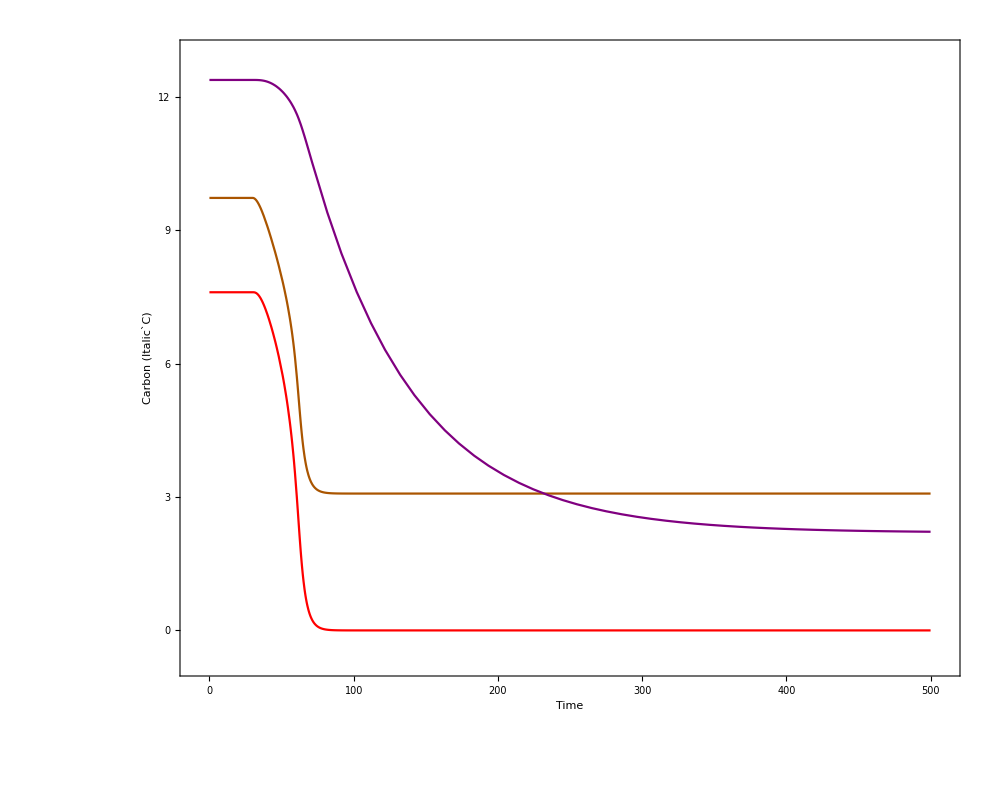
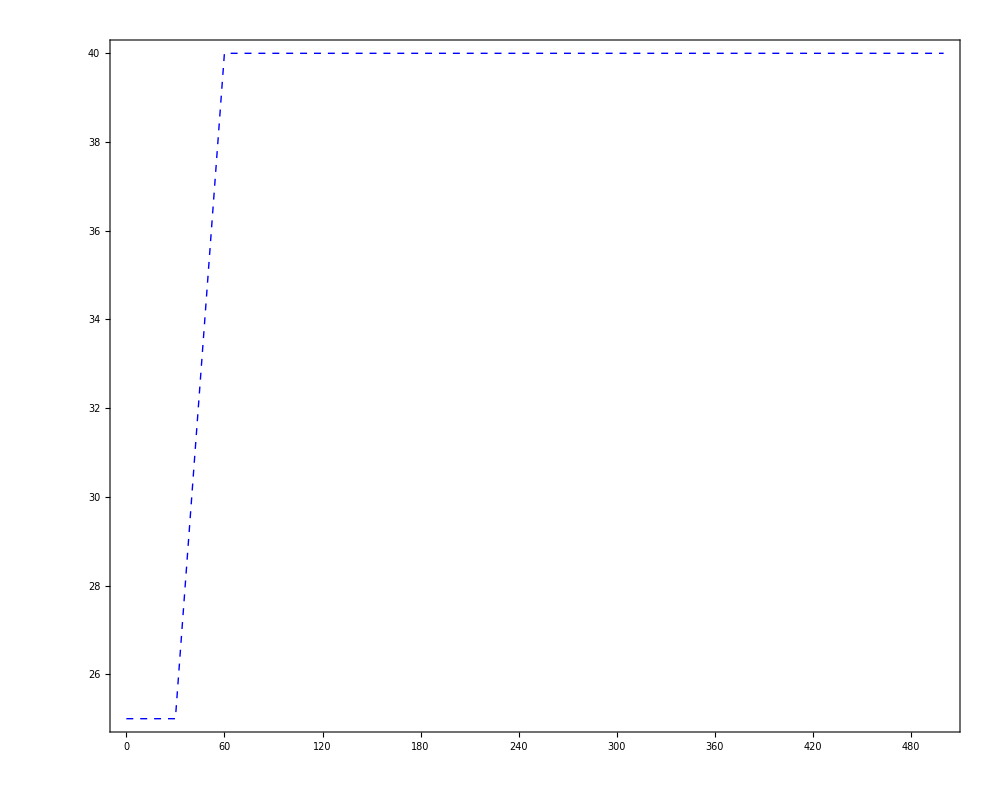

```mathematica
Module[{plt,sol,xrange,rmax,k,ma,mh,shh,pda,pea,pba,alpha,hca,beta,pbs,pes,pds,pdb,hmax0,hmax1,t0,t1,s0,ca0,cs0,cb0,solexist,deriv,test,stableSolutions,greatestStableSolution},

rmax=6/5;
k=6;
mh=1/20;
shh=1;
ma=1/4;
pda=0.05;
pea=0.2;
pba=0.01;
alpha=4;
hca=10;
beta=0.6;
pbs=0.01;
pes=0.2;
pds=0.05;
pdb=0.014;

xrange=500;
t0=30;
t1=60;

hmax0=25;
hmax1=40;
ds=rmax*s*(1-s/k)-s*(ma+mh*hmax0*shh/(shh+s));
sol=Solve[{ds==0,Element[s,Reals]},{s}];
solexist=Select[sol,(#[[1,2]]>=0)&];
deriv=D[ds,s]/. solexist;
test=Map[#<=0&,deriv];
stableSolutions=Pick[solexist,test];
s0=MaximalBy[stableSolutions,#[[1,2]]&][[1,1,2]];
ca0=1/(pda+pea+pba)*(alpha*hca/(hca+hmax0*shh/(shh+s0)));
cs0=beta*s0/(pds+pes+pbs);
cb0=(pba*ca0+pbs*cs0)/pdb;

solint=NDSolve[{s'[t]==rmax*s[t]*(1-s[t]/k)-s[t]*(ma+mh*hmax[t]*shh/(shh+s[t])),ca'[t]==alpha*hca/(hca+(hmax[t]*shh/(shh+s[t])))-ca[t]*(pda+pea+pba),cs'[t]==beta*s[t]-cs[t]*(pds+pes+pbs),cb'[t]==pba*ca[t]+pbs*cs[t]-pdb*cb[t],hmax'[t]==Piecewise[{{0,0<=t<t0},{(hmax1-hmax0)/(t1-t0),t0<=t<t1},{0,t>=t1}}],s[0]==s0,ca[0]==ca0,cs[0]==cs0,cb[0]==cb0,hmax[0]==hmax0},{s,ca,cs,cb,hmax},{t,0,xrange}];

stPlot=Plot[Evaluate[{ca[t]/. solint,cs[t]/. solint,cb[t]/. solint}],{t,0,xrange},PlotStyle->{Darker[Orange],Red,Purple},ImagePadding->50,Frame->{True,True,True,False},FrameLabel->{Style["Time",16,Black],Style["Carbon (\!\(\*Italic\`C\))",16,Black]}
,FrameTicks->{{{0,3,6,9,12},None},{{0,100,200,300,400,500},None}},FrameTicksStyle->Directive[FontSize->14],Axes->False,PlotRange->{{-10,510},{-0.75,13}},AspectRatio->0.8,ImageSize->{1000,500}];

hmaxPlot=Plot[Evaluate[hmax[t]/. solint],{t,0,xrange},PlotStyle->{Thick,Dashed,Blue},ImagePadding->50,Frame->{False,False,False,True},FrameTicks->{{None,{25,30,35,40}},{None,None}},FrameStyle->{Automatic,Automatic,Automatic,Automatic},ImageSize->{1000,500},FrameLabel->{{None,Row[{Style["Maximum hydrodynamic (",16,Blue],Style[Subscript[H,max],16,Blue,Italic],Style[")",16,Blue]}]},{None,None}},FrameTicksStyle->Directive[FontSize->14],AspectRatio->0.8];
fusion2=Overlay[{stPlot,hmaxPlot}]]
```

```mathematica
Export["",fusion2,ImageResolution->1000];
```

### Abrupt ma change

#### Seagrass

```mathematica
Clear[plt,sol,xrange,rmax,k,hmax,mh,shh,ma0,ma1,t0,t1,s0,solexist,deriv,test,stableSolutions,greatestStableSolution,s,ma]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

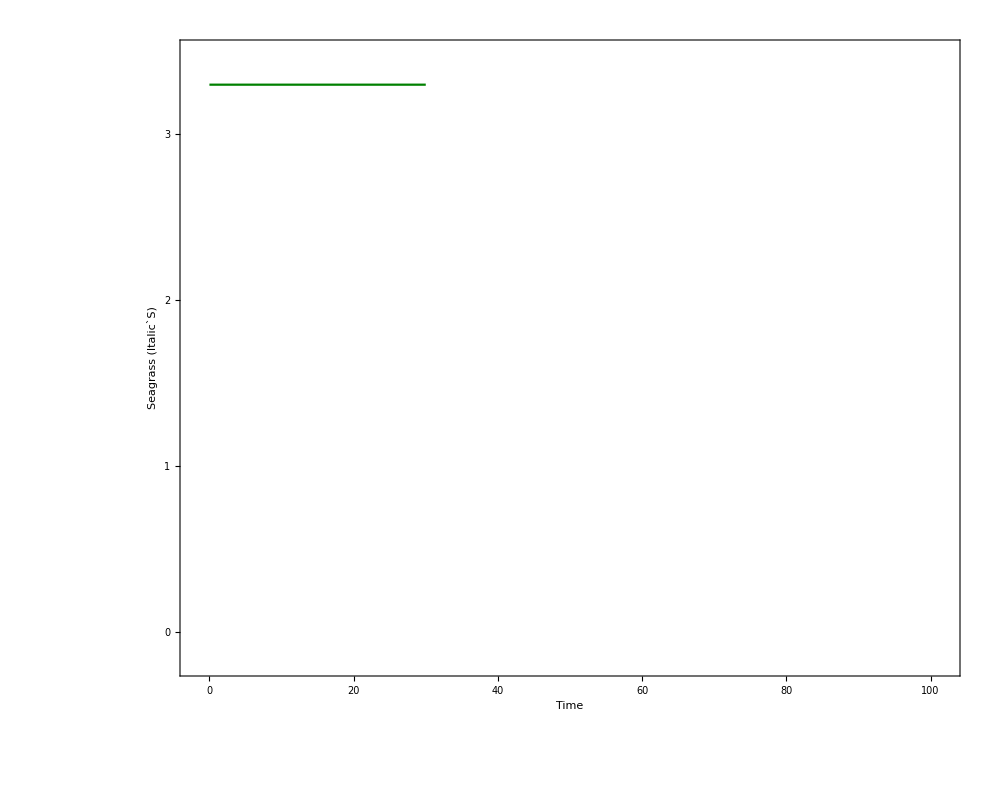
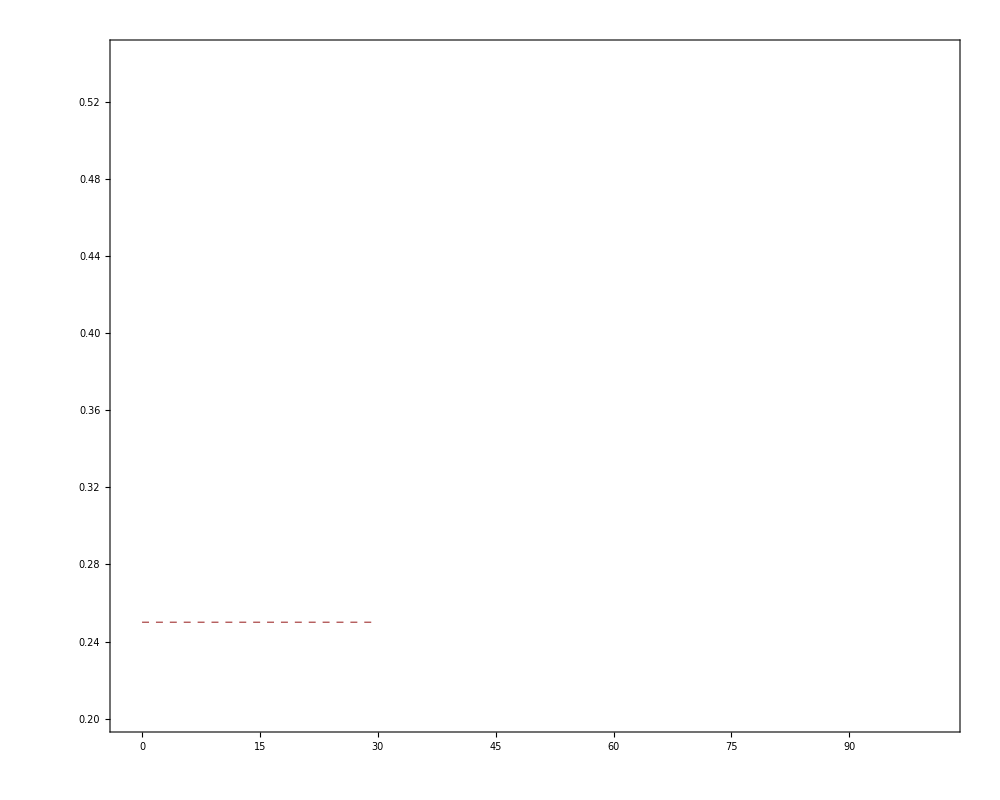

```mathematica
Module[{plt,sol,xrange,rmax,k,hmax,mh,shh,ma0,ma1,t0,t1,s0,solexist,deriv,test,stableSolutions,greatestStableSolution},

rmax=6/5;
k=6;
mh=1/20;
shh=1;
hmax=25;

xrange=100;
t0=30;
t1=60;
ma0=0.25;
ma1=0.5;

ds=rmax*s*(1-s/k)-s*(ma0+mh*hmax*shh/(shh+s));
sol=Solve[{ds==0,Element[s,Reals]},{s}];
solexist=Select[sol,(#[[1,2]]>=0)&];
deriv=D[ds,s]/. solexist;
test=Map[#<=0&,deriv];
stableSolutions=Pick[solexist,test];
s0=MaximalBy[stableSolutions,#[[1,2]]&][[1,1,2]];

solint=NDSolve[{s'[t]==rmax*s[t]*(1-s[t]/k)-s[t]*(ma0+mh*hmax*shh/(shh+s[t])),ma'[t]==0,s[0]==s0,ma[0]==ma0},{s,ma},{t,0,t0}];

stPlot=Plot[Evaluate[s[t]/. solint],{t,0,t0},PlotStyle->Darker[Green,0.5],ImagePadding->50,Frame->{True,True,True,False},FrameLabel->{Style["Time",16,Black],Style["Seagrass (\!\(\*Italic\`S\))",16,Darker[Green,0.5]]}
,FrameTicks->{{{0,1,2,3},None},{{0,20,40,60,80,100},None}},FrameTicksStyle->Directive[FontSize->14],Axes->False,PlotRange->{{-2,102},{-0.19,3.49}},AspectRatio->0.8,ImageSize->{1000,500}];

maPlot=Plot[Evaluate[ma[t]/. solint],{t,0,t0},PlotStyle->{Thick,Dashed,Darker[Pink,0.3]},ImagePadding->50,Frame->{False,False,False,True},FrameTicks->{{None,{0.25,0.30,0.40,0.5}},{None,None}},FrameStyle->{Automatic,Automatic,Automatic,Automatic},ImageSize->{1000,500},PlotRange->{{-2,102},{0.2,0.545}},FrameLabel->{{None,Row[{Style["Anthropogenic pressures (",16,Darker[Pink,0.3]],Style[Subscript[m,A],16,Darker[Pink,0.3],Italic],Style[")",16,Darker[Pink,0.3]]}]},{None,None}},FrameTicksStyle->Directive[FontSize->14],AspectRatio->0.8];
fusion3=Overlay[{stPlot,maPlot}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

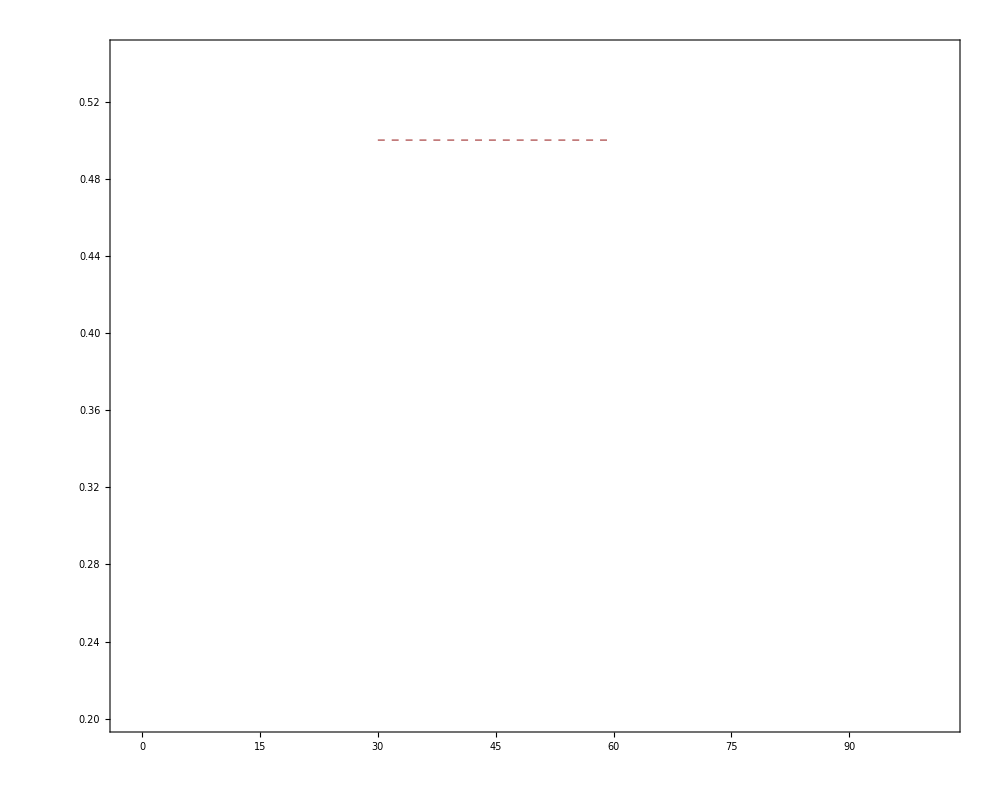
-Graphics--Graphics-

```mathematica
Module[{plt,sol,xrange,rmax,k,hmax,mh,shh,ma0,ma1,t0,t1,s0,solexist,deriv,test,stableSolutions,greatestStableSolution},

rmax=6/5;
k=6;
mh=1/20;
shh=1;
hmax=25;

xrange=100;
t0=30;
t1=60;
ma0=0.25;
ma1=0.5;

ds=rmax*s*(1-s/k)-s*(ma0+mh*hmax*shh/(shh+s));
sol=Solve[{ds==0,Element[s,Reals]},{s}];
solexist=Select[sol,(#[[1,2]]>=0)&];
deriv=D[ds,s]/. solexist;
test=Map[#<=0&,deriv];
stableSolutions=Pick[solexist,test];
s0=MaximalBy[stableSolutions,#[[1,2]]&][[1,1,2]];

solint=NDSolve[{s'[t]==rmax*s[t]*(1-s[t]/k)-s[t]*(ma[t]+mh*hmax*shh/(shh+s[t])),ma'[t]==0,s[t0]==s0,ma[t0]==ma1},{s,ma},{t,t0,t1}];

stPlot=Plot[Evaluate[s[t]/. solint],{t,t0,t1},PlotStyle->Darker[Green,0.5],ImagePadding->50,Frame->{False,False,False,False}
,FrameTicks->{{None,None},{None,None}},FrameTicksStyle->Directive[FontSize->14],Axes->False,PlotRange->{{-2,102},{-0.19,3.49}},AspectRatio->0.8,ImageSize->{1000,500}];

maPlot=Plot[Evaluate[ma[t]/. solint],{t,t0,t1},PlotStyle->{Thick,Dashed,Darker[Pink,0.3]},ImagePadding->50,Frame->{False,False,False,True},FrameTicks->{{None,None},{None,None}},FrameStyle->{Automatic,Automatic,Automatic,Automatic},ImageSize->{1000,500},PlotRange->{{-2,102},{0.2,0.545}},FrameTicksStyle->Directive[FontSize->14],AspectRatio->0.8];
fusion4=Overlay[{stPlot,maPlot}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

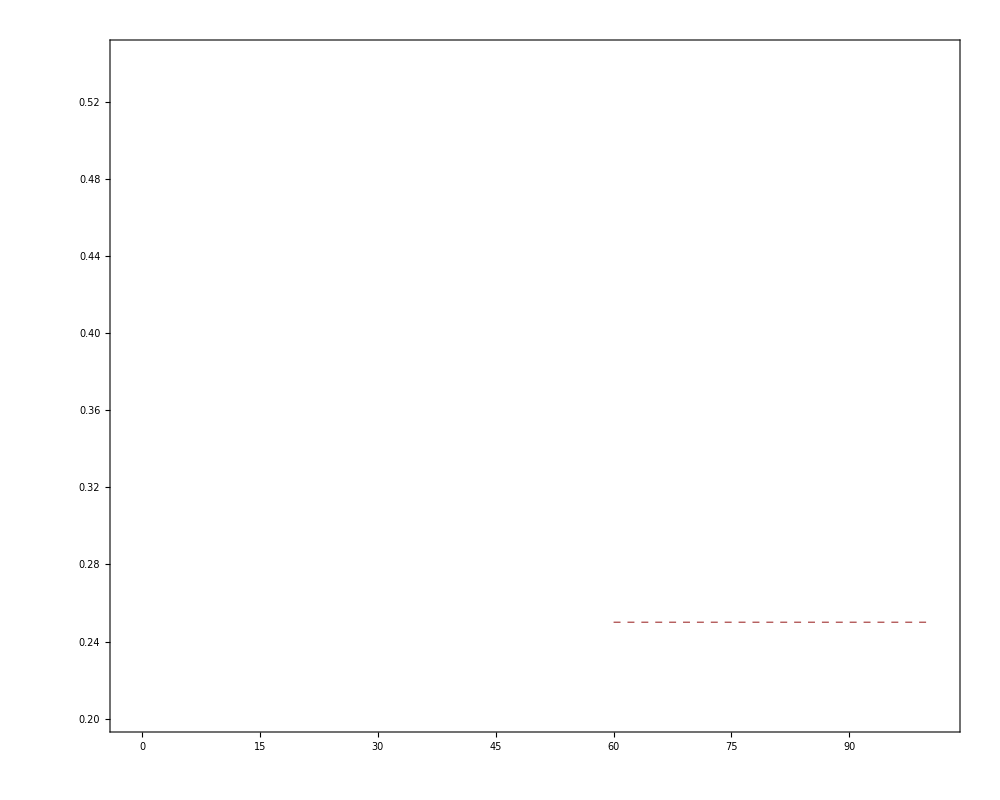
-Graphics--Graphics-

```mathematica
Module[{plt,sol,xrange,rmax,k,hmax,mh,shh,ma0,ma1,t0,t1,s0,solexist,deriv,test,stableSolutions,greatestStableSolution},

rmax=6/5;
k=6;
mh=1/20;
shh=1;
hmax=25;

xrange=100;
t0=30;
t1=60;
ma0=0.25;
ma1=0.5;

ds=rmax*s*(1-s/k)-s*(ma1+mh*hmax*shh/(shh+s));
sol=Solve[{ds==0,Element[s,Reals]},{s}];
solexist=Select[sol,(#[[1,2]]>=0)&];
deriv=D[ds,s]/. solexist;
test=Map[#<=0&,deriv];
stableSolutions=Pick[solexist,test];
s0=MaximalBy[stableSolutions,#[[1,2]]&][[1,1,2]];

solint=NDSolve[{s'[t]==rmax*s[t]*(1-s[t]/k)-s[t]*(ma[t]+mh*hmax*shh/(shh+s[t])),ma'[t]==0,s[t1]==s0,ma[t1]==ma0},{s,ma},{t,t1,xrange}];

stPlot=Plot[Evaluate[s[t]/. solint],{t,t1,xrange},PlotStyle->Darker[Green,0.5],ImagePadding->50,Frame->{False,False,False,False}
,FrameTicks->{{None,None},{None,None}},FrameTicksStyle->Directive[FontSize->14],Axes->False,PlotRange->{{-2,102},{-0.19,3.49}},AspectRatio->0.8,ImageSize->{1000,500}];

maPlot=Plot[Evaluate[ma[t]/. solint],{t,t1,xrange},PlotStyle->{Thick,Dashed,Darker[Pink,0.3]},ImagePadding->50,Frame->{False,False,False,True},FrameTicks->{{None,None},{None,None}},FrameStyle->{Automatic,Automatic,Automatic,Automatic},ImageSize->{1000,500},PlotRange->{{-2,102},{0.2,0.545}},FrameTicksStyle->Directive[FontSize->14],AspectRatio->0.8];
fusion5=Overlay[{stPlot,maPlot}]]
```

```mathematica
fusion6 =Overlay[{fusion3,fusion4,fusion5}]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Export["",fusion6,ImageResolution->1000];
```

#### Carbon

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

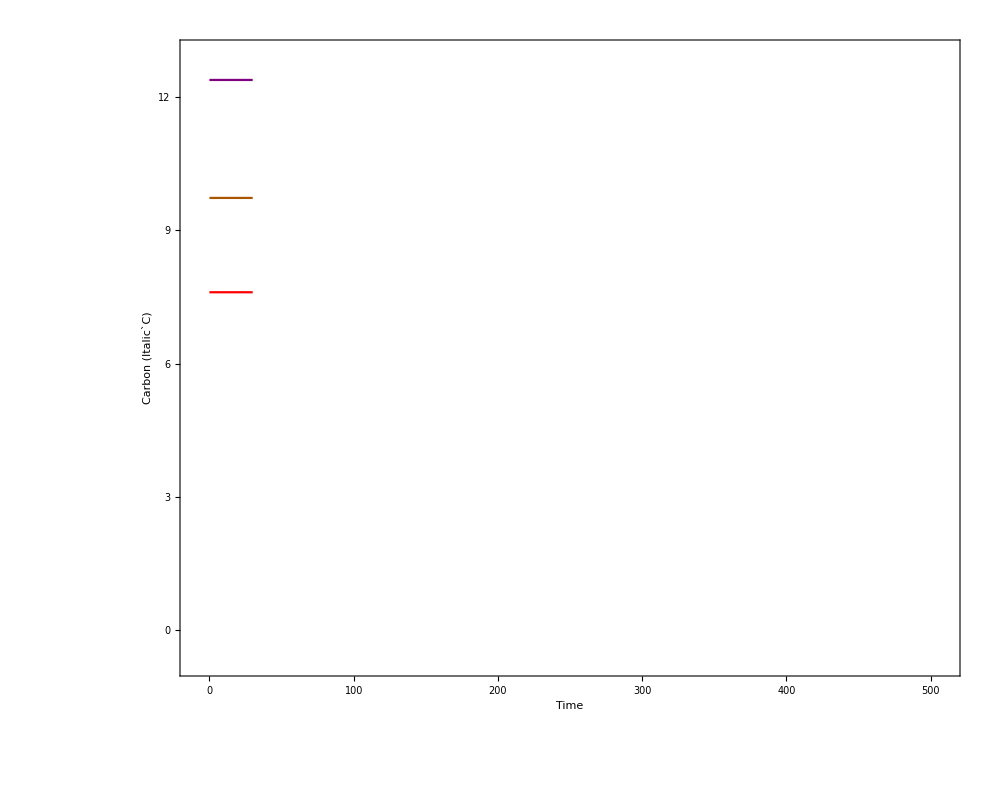
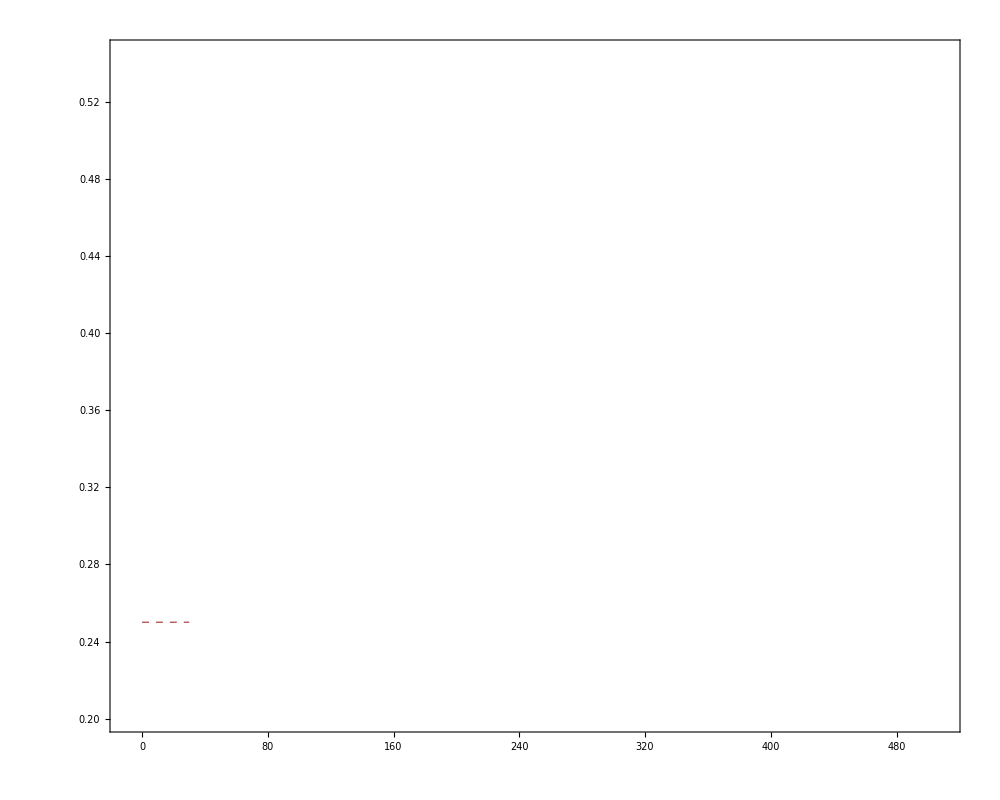

```mathematica
Module[{plt,sol,xrange,rmax,k,hmax,mh,shh,ma0,ma1,t0,t1,s0,ca0,cs0,cb0,solexist,deriv,test,stableSolutions,greatestStableSolution,pda,pea,pba,alpha,hca,beta,pbs,pes,pds,pdb},

rmax=6/5;
k=6;
mh=1/20;
shh=1;
hmax=25;
pda=0.05;
pea=0.2;
pba=0.01;
alpha=4;
hca=10;
beta=0.6;
pbs=0.01;
pes=0.2;
pds=0.05;
pdb=0.014;

xrange=500;
t0=30;
t1=60;
ma0=0.25;
ma1=0.5;

ds=rmax*s*(1-s/k)-s*(ma0+mh*hmax*shh/(shh+s));
sol=Solve[{ds==0,Element[s,Reals]},{s}];
solexist=Select[sol,(#[[1,2]]>=0)&];
deriv=D[ds,s]/. solexist;
test=Map[#<=0&,deriv];
stableSolutions=Pick[solexist,test];
s0=MaximalBy[stableSolutions,#[[1,2]]&][[1,1,2]];
ca0=1/(pda+pea+pba)*(alpha*hca/(hca+hmax*shh/(shh+s0)));
cs0=beta*s0/(pds+pes+pbs);
cb0=(pba*ca0+pbs*cs0)/pdb;

solint=NDSolve[{s'[t]==rmax*s[t]*(1-s[t]/k)-s[t]*(ma[t]+mh*hmax*shh/(shh+s[t])),ca'[t]==alpha*hca/(hca+(hmax*shh/(shh+s[t])))-ca[t]*(pda+pea+pba),cs'[t]==beta*s[t]-cs[t]*(pds+pes+pbs),cb'[t]==pba*ca[t]+pbs*cs[t]-pdb*cb[t],ma'[t]==0,ca[0]==ca0,cs[0]==cs0,cb[0]==cb0,s[0]==s0,ma[0]==ma0},{s,ca,cs,cb,ma},{t,0,t0}];

stPlot=Plot[Evaluate[{ca[t]/. solint,cs[t]/. solint,cb[t]/. solint}],{t,0,t0},PlotStyle->{Darker[Orange],Red,Purple},ImagePadding->50,Frame->{True,True,True,False},FrameLabel->{Style["Time",16,Black],Style["Carbon (\!\(\*Italic\`C\))",16,Black]}
,FrameTicks->{{{0,3,6,9,12},None},{{0,100,200,300,400,500},None}},FrameTicksStyle->Directive[FontSize->14],Axes->False,PlotRange->{{-10,510},{-0.75,13}},AspectRatio->0.8,ImageSize->{1000,500}];

maPlot=Plot[Evaluate[ma[t]/. solint],{t,0,t0},PlotStyle->{Thick,Dashed,Darker[Pink,0.3]},ImagePadding->50,Frame->{False,False,False,True},FrameTicks->{{None,{0.25,0.30,0.40,0.5}},{None,None}},FrameStyle->{Automatic,Automatic,Automatic,Automatic},ImageSize->{1000,500},PlotRange->{{-10,510},{0.2,0.545}},FrameLabel->{{None,Row[{Style["Anthropogenic pressures (",16,Darker[Pink,0.3]],Style[Subscript[m,A],16,Darker[Pink,0.3],Italic],Style[")",16,Darker[Pink,0.3]]}]},{None,None}},FrameTicksStyle->Directive[FontSize->14],AspectRatio->0.8];
fusion7=Overlay[{stPlot,maPlot}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

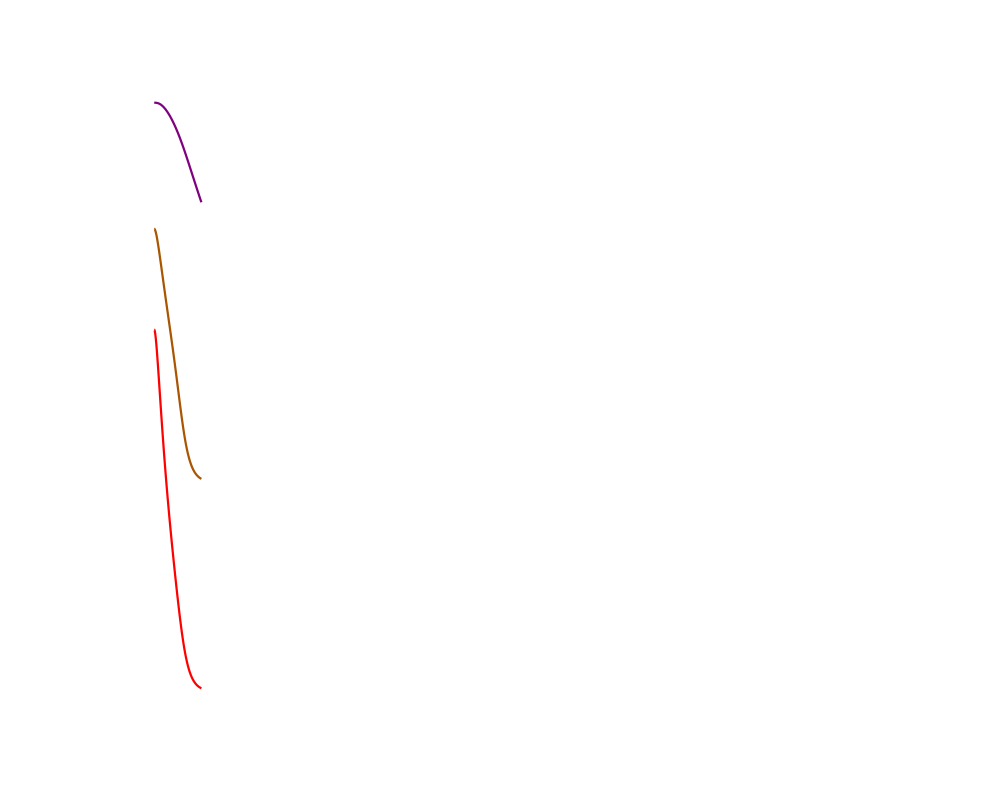
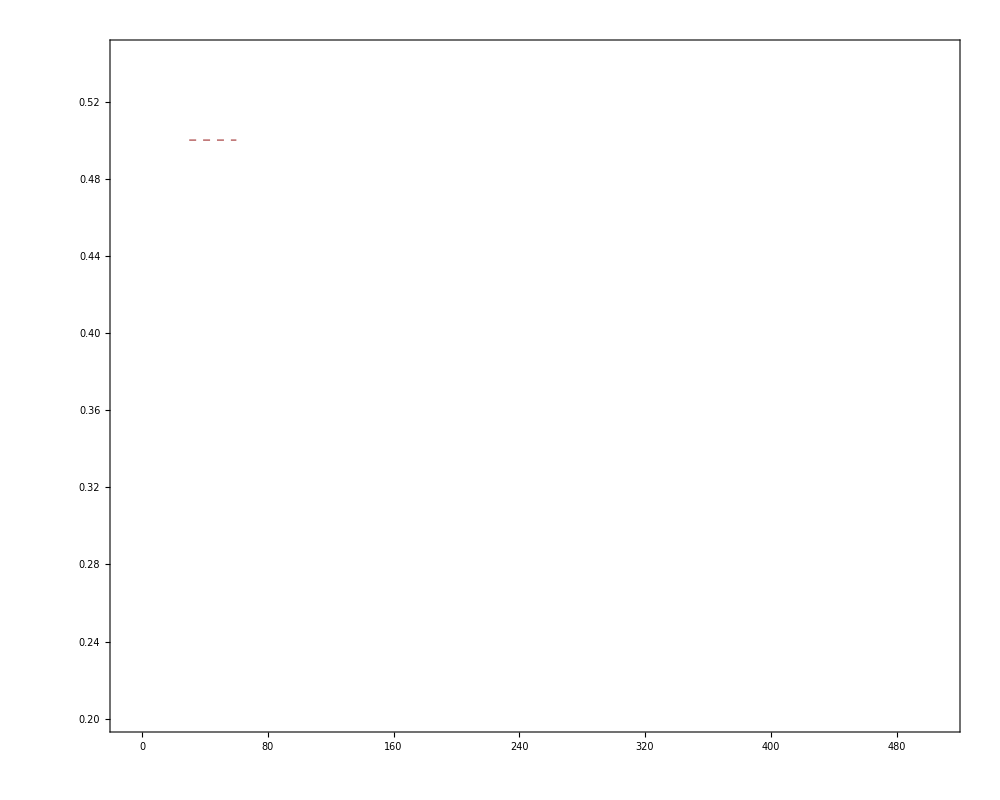

```mathematica
Module[{plt,sol,xrange,rmax,k,hmax,mh,shh,ma0,ma1,t0,t1,s0,ca0,cs0,cb0,solexist,deriv,test,stableSolutions,greatestStableSolution,pda,pea,pba,alpha,hca,beta,pbs,pes,pds,pdb},

rmax=6/5;
k=6;
mh=1/20;
shh=1;
hmax=25;
pda=0.05;
pea=0.2;
pba=0.01;
alpha=4;
hca=10;
beta=0.6;
pbs=0.01;
pes=0.2;
pds=0.05;
pdb=0.014;

xrange=500;
t0=30;
t1=60;
ma0=0.25;
ma1=0.5;

ds=rmax*s*(1-s/k)-s*(ma0+mh*hmax*shh/(shh+s));
sol=Solve[{ds==0,Element[s,Reals]},{s}];
solexist=Select[sol,(#[[1,2]]>=0)&];
deriv=D[ds,s]/. solexist;
test=Map[#<=0&,deriv];
stableSolutions=Pick[solexist,test];
s0=MaximalBy[stableSolutions,#[[1,2]]&][[1,1,2]];
ca0=1/(pda+pea+pba)*(alpha*hca/(hca+hmax*shh/(shh+s0)));
cs0=beta*s0/(pds+pes+pbs);
cb0=(pba*ca0+pbs*cs0)/pdb;

solint=NDSolve[{s'[t]==rmax*s[t]*(1-s[t]/k)-s[t]*(ma[t]+mh*hmax*shh/(shh+s[t])),ca'[t]==alpha*hca/(hca+(hmax*shh/(shh+s[t])))-ca[t]*(pda+pea+pba),cs'[t]==beta*s[t]-cs[t]*(pds+pes+pbs),cb'[t]==pba*ca[t]+pbs*cs[t]-pdb*cb[t],ma'[t]==0,ca[t0]==ca0,cs[t0]==cs0,cb[t0]==cb0,s[t0]==s0,ma[t0]==ma1},{s,ca,cs,cb,ma},{t,t0,t1}];

stPlot=Plot[Evaluate[{ca[t]/. solint,cs[t]/. solint,cb[t]/. solint}],{t,t0,t1},PlotStyle->{Darker[Orange],Red,Purple},ImagePadding->50,Frame->{False,False,False,False},FrameLabel->{Style["Time",16,Black],Style["Seagrass (\!\(\*Italic\`S\))",16,Darker[Green,0.5]]}
,FrameTicks->{{None,None},{None,None}},FrameTicksStyle->Directive[FontSize->14],Axes->False,PlotRange->{{-10,510},{-0.75,13}},AspectRatio->0.8,ImageSize->{1000,500}];

maPlot=Plot[Evaluate[ma[t]/. solint],{t,t0,t1},PlotStyle->{Thick,Dashed,Darker[Pink,0.3]},ImagePadding->50,Frame->{False,False,False,True},FrameTicks->{{None,None},{None,None}},FrameStyle->{Automatic,Automatic,Automatic,Automatic},ImageSize->{1000,500},PlotRange->{{-10,510},{0.2,0.545}},FrameTicksStyle->Directive[FontSize->14],AspectRatio->0.8];
fusion8=Overlay[{stPlot,maPlot}]]
```

```mathematica
casave = ca[60]/. solint
cssave = cs[60]/. solint
cbsave = cb[60]/. solint
```

{4.46624}

{0.0620488}

{10.2831}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

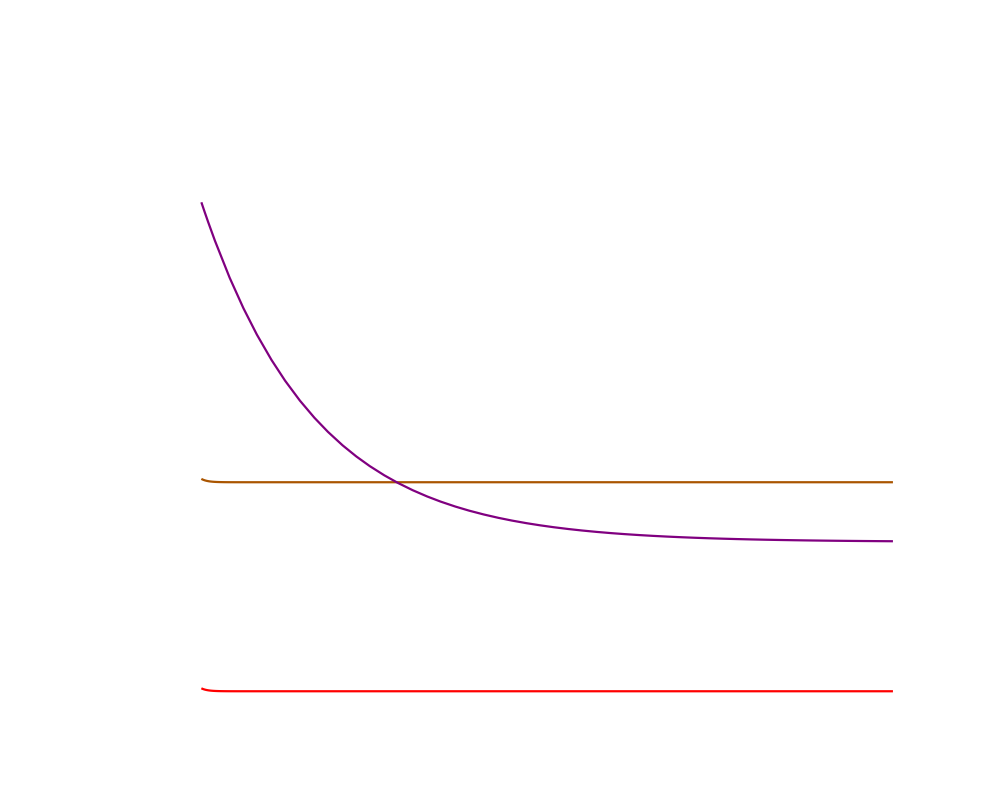
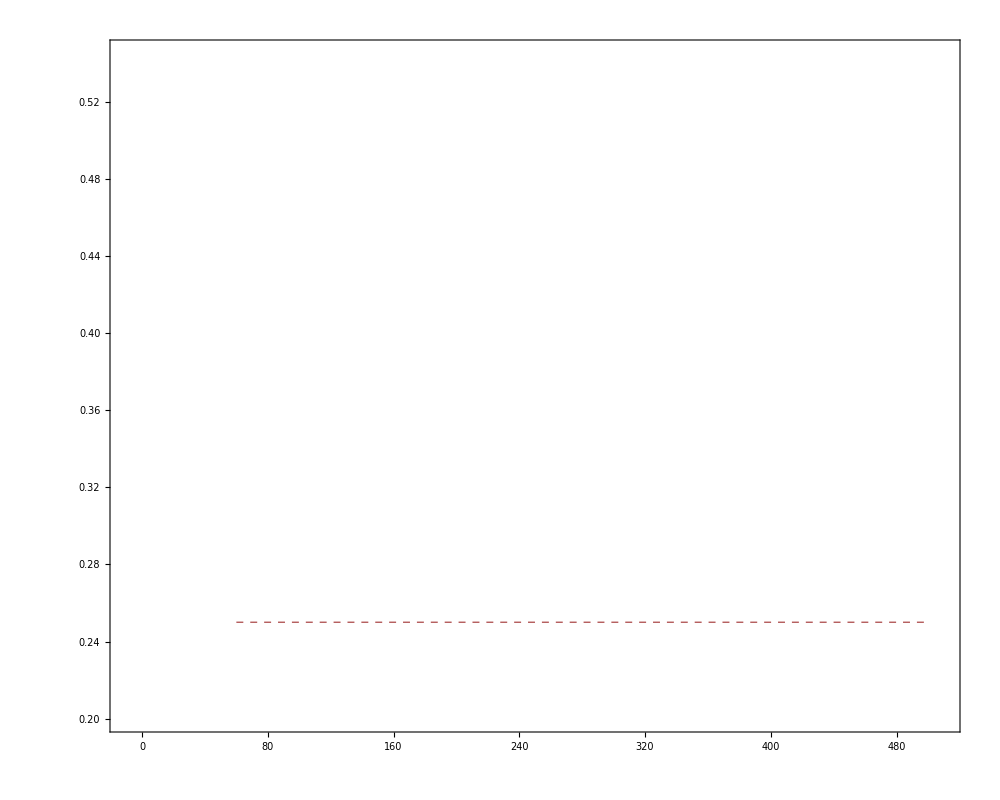

```mathematica
Module[{plt,sol,xrange,rmax,k,hmax,mh,shh,ma0,ma1,t0,t1,s0,ca0,cs0,cb0,solexist,deriv,test,stableSolutions,greatestStableSolution,pda,pea,pba,alpha,hca,beta,pbs,pes,pds,pdb},

rmax=6/5;
k=6;
mh=1/20;
shh=1;
hmax=25;
pda=0.05;
pea=0.2;
pba=0.01;
alpha=4;
hca=10;
beta=0.6;
pbs=0.01;
pes=0.2;
pds=0.05;
pdb=0.014;

xrange=500;
t0=30;
t1=60;
ma0=0.25;
ma1=0.5;

ds=rmax*s*(1-s/k)-s*(ma1+mh*hmax*shh/(shh+s));
sol=Solve[{ds==0,Element[s,Reals]},{s}];
solexist=Select[sol,(#[[1,2]]>=0)&];
deriv=D[ds,s]/. solexist;
test=Map[#<=0&,deriv];
stableSolutions=Pick[solexist,test];
s0=MaximalBy[stableSolutions,#[[1,2]]&][[1,1,2]];
ca0=casave;
cs0=cssave;
cb0=cbsave;

solint=NDSolve[{s'[t]==rmax*s[t]*(1-s[t]/k)-s[t]*(ma[t]+mh*hmax*shh/(shh+s[t])),ca'[t]==alpha*hca/(hca+(hmax*shh/(shh+s[t])))-ca[t]*(pda+pea+pba),cs'[t]==beta*s[t]-cs[t]*(pds+pes+pbs),cb'[t]==pba*ca[t]+pbs*cs[t]-pdb*cb[t],ma'[t]==0,ca[t1]==ca0,cs[t1]==cs0,cb[t1]==cb0,s[t1]==s0,ma[t1]==ma0},{s,ca,cs,cb,ma},{t,t1,xrange}];

stPlot=Plot[Evaluate[{ca[t]/. solint,cs[t]/. solint,cb[t]/. solint}],{t,t1,xrange},PlotStyle->{Darker[Orange],Red,Purple},ImagePadding->50,Frame->{False,False,False,False},FrameLabel->{Style["Time",16,Black],Style["Seagrass (\!\(\*Italic\`S\))",16,Darker[Green,0.5]]}
,FrameTicks->{{None,None},{None,None}},FrameTicksStyle->Directive[FontSize->14],Axes->False,PlotRange->{{-10,510},{-0.75,13}},AspectRatio->0.8,ImageSize->{1000,500}];

maPlot=Plot[Evaluate[ma[t]/. solint],{t,t1,xrange},PlotStyle->{Thick,Dashed,Darker[Pink,0.3]},ImagePadding->50,Frame->{False,False,False,True},FrameTicks->{{None,None},{None,None}},FrameStyle->{Automatic,Automatic,Automatic,Automatic},ImageSize->{1000,500},PlotRange->{{-10,510},{0.2,0.545}},FrameTicksStyle->Directive[FontSize->14],AspectRatio->0.8];
fusion9=Overlay[{stPlot,maPlot}]]
```

```mathematica
fusion10=Overlay[{fusion7,fusion8,fusion9}]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Export["",fusion10,ImageResolution->1000];
```